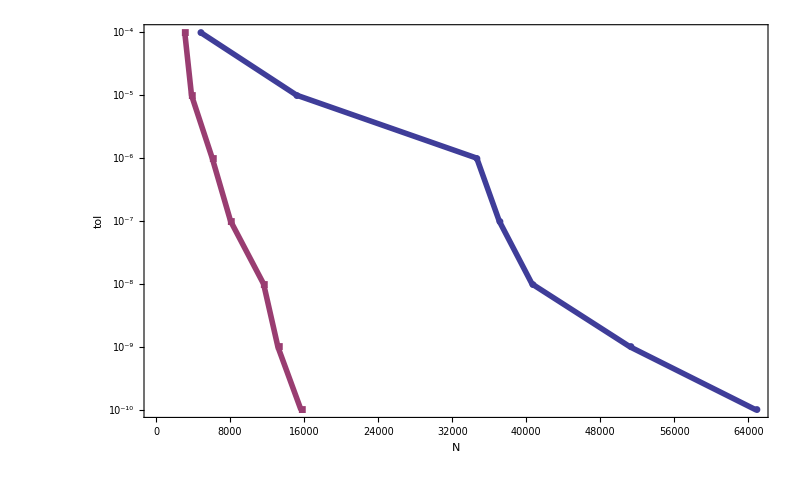

E:\university\diploma\docs\tex\pics\num_ex_1_1.pdf

```mathematica
(*1_1*)
NN={4,5,6,7,8,9,10};
NN=10.^-#&/@NN;

simple={4782,15193,34652,37083,40628,51231,64823};
opress5={3104,3835,6074,8056,11627,13173,15666};
opress7={2788,3564,5978,6928,11008,13111,13852};
(*opress10={2895,3797,6076,6545,10436,12072,14811};*)
opress15={2947,3882,5773,7062,9712,12355,15790};
opress30={2789,4452,7189,6978,9694,13875,18785};

Needs["PlotLegends`"]
gp[NN_,arr_]:=Partition[Riffle[NN,arr],2];
(*gp[opress7,NN], gp[opress10,NN], gp[opress15,NN], gp[opress30,NN]*)
(* Style["OPR7",20,Bold], Style["OPR15",20,Bold], Style["OPR30",20,Bold]*)
g1=ListLogPlot[{gp[simple,NN],gp[opress5,NN]},LabelStyle->Directive[Bold,FontSize->20,Black],Frame->True,PlotMarkers->Automatic ,Joined->True,PlotStyle->{{Directive[PointSize[.4]],Thickness[0.005]}},Axes->False,PlotLegend->{Style["SP",20,Bold],Style["OPR5",20,Bold]},LegendPosition->{1.1,-0.4},Joined->{True,True,False},PlotMarkers->Automatic,FrameLabel->{"N","tol"},LegendSize->0.5,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->800, PlotRange->All]
Export["E:\\university\\diploma\\docs\\tex\\pics\\num_ex_1_1.pdf",g1]
```

```mathematica
NN//ScientificForm
```

{1.×10^-4,1.×10^-5,1.×10^-6,1.×10^-7,1.×10^-8,1.×10^-9,1.×10^-10}

```mathematica
Options[ListPlot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→False,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}}

```mathematica
10^10
```

10000000000